```mathematica
dist =MixtureDistribution[{1,1},{NormalDistribution[100,8],NormalDistribution[100,30]}];
```

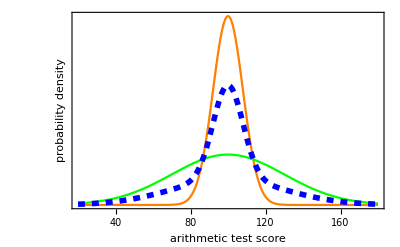

```mathematica
g1=Plot[{PDF[NormalDistribution[100,8],x],PDF[NormalDistribution[100,30],x],PDF[dist,x]},{x,20,180},PlotRange->Full,PlotStyle->{Orange,Green,{Dashed,Blue,Thickness[0.01]}},AxesOrigin->{20,0},Frame->{True,True,False,False},FrameLabel->{"arithmetic test score","probability density"},FrameTicks->{True,False},BaseStyle->Medium]
```

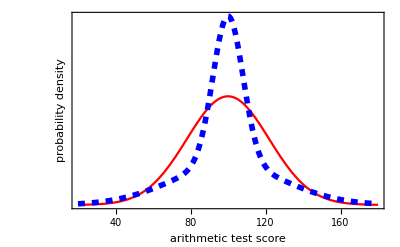

```mathematica
g2=Plot[{PDF[NormalDistribution[100,Sqrt@Variance@dist],x],PDF[dist,x]},{x,20,180},AxesOrigin->{20,0},Frame->{True,True,False,False},FrameLabel->{"arithmetic test score","probability density"},FrameTicks->{True,False},BaseStyle->Medium,PlotStyle->{Red,{Dashed,Blue,Thickness[0.01]}},PlotRange->Full]
```

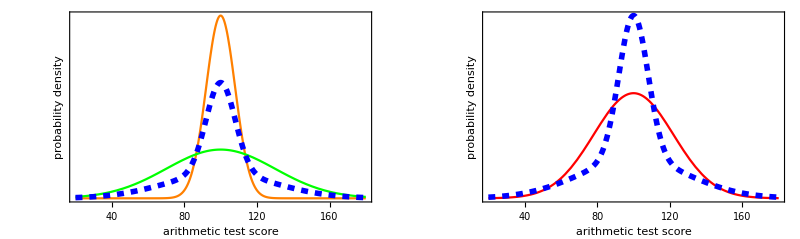

```mathematica
gFinal=Show[GraphicsRow[{g1,g2}],ImageSize->800]
```

```mathematica
Export["Distributions_tArithmeticDispersion.pdf",gFinal]
```

Distributions_tArithmeticDispersion.pdf